```mathematica
Clear[λ0,δλ,β]
λ[t_]=λ0+δλ t/τ;
H[q_,p_,t_]=p^2/2+λ[t]q^2/2;

sol=FullSimplify[DSolve[{q'[t]== p[t],p'[t]== -λ[t]q[t],q[0]==q0,p[0]==p0},{q[t],p[t]},t]];

q1[t_]=q[t]/.sol[[1,2]];
p1[t_]=p[t]/.sol[[1,1]];
```

0.25

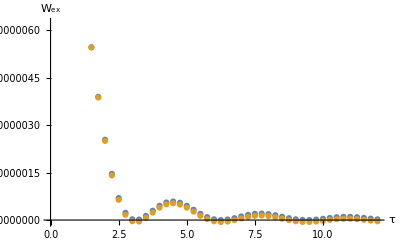

```mathematica
Clear[λ0,δλ,β]

δλ=0.01;
β=1;
λ0=1;

(* EXCESS WORK *)

W[q0_,p0_]=Expand[H[q1[τ],p1[τ],τ]-H[q1[0],p1[0],0]];

partition=Assuming[{β>0,λ0>0},Integrate[Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]];
a1=Assuming[{β>0,λ0>0},Integrate[q0 p0 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a2=Assuming[{β>0,λ0>0},Integrate[q0^2 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a3=Assuming[{β>0,λ0>0},Integrate[p0^2 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;

Wm[τ_]=Expand[W[q0,p0]]/.{p0 q0-> a1,p0 π^2 q0->π^2 a1,p0 π q0->π a1,q0^2-> a2,p0^2-> a3};
Wex[τ_]=Wm[τ]-(√(1+δλ/λ0)-1)/β;

data1=Table[{τ,Wex[τ]},{τ,0.001,12.1,0.25}];

(* VARIANCE OF WORK *)

W21[q0_,p0_]=Expand[(W[q0,p0]-Wm[τ])^2];

a4=Assuming[{β>0,λ0>0},Integrate[p0^4 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a5=Assuming[{β>0,λ0>0},Integrate[q0^4 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a6=Assuming[{β>0,λ0>0},Integrate[p0^2q0^2 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a7=Assuming[{β>0,λ0>0},Integrate[p0^3q0 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;
a8=Assuming[{β>0,λ0>0},Integrate[p0 q0^3 Exp[-β H[q0,p0,0]],{q0,-Infinity,Infinity},{p0,-Infinity,Infinity}]]/partition;

varW[τ_]=Expand[W21[q0,p0]]/.{p0 q0-> a1,p0 π^2 q0->π^2 a1,p0 π q0->π a1,q0^2-> a2,p0^2-> a3,p0^4-> a4,q0^4-> a5,p0^2 π^4 q0^2->a6 π^4,p0^3 π^4 q0-> a7 π^4,p0^3 q0-> a7 ,p0 π^4 q0^3-> a8 π^4,p0 q0^3-> a8 ,p0^2 π^3 q0^2->a6 π^3,p0^2 q0^2->a6,p0^3 π^3 q0-> a7 π^3,p0 π^3 q0^3-> a8 π^3};

varWqs=1/8(a5-a2^2)

data2=Table[{τ,varW[τ]/2-(δλ^2 varWqs)/2},{τ,0.001,12.1,0.25}];

plotWex=ListPlot[{data1,data2},AxesLabel->{"τ","W_ex"}]

Export["Research/ongoing/VTILR/data/dataWex.dat",data1];
Export["Research/ongoing/VTILR/data/dataVar.dat",data2];
```

Optimal variance and optimal work distribution

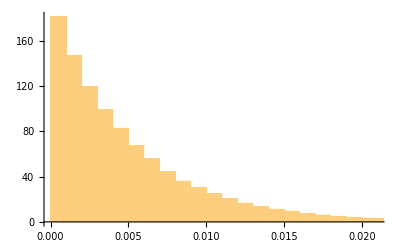

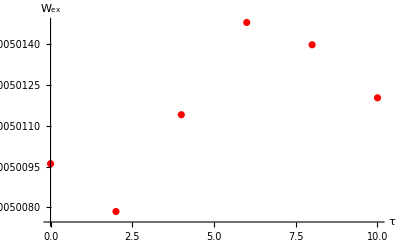

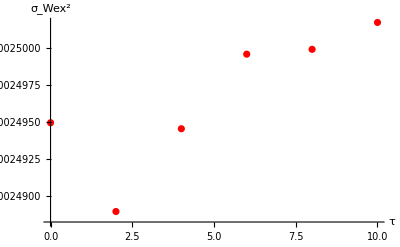

```mathematica
Clear[n,λ0,δλ,β,qi,pi];

n=100000;
step=2;

β=1;
λ0=1;
δλ=0.01;

(*data4=List[];*)
data5=List[];
data6=List[];

Do[

Do[

qi=RandomVariate[NormalDistribution[0,1/(β λ0)]];
pi=RandomVariate[NormalDistribution[0,1/β ]];

Wqs=δλ/(2 λ0) (pi^2/2+(qi^2 λ0)/2);

data4=AppendTo[data4,Wqs];

,{i,1,n}];

data5=AppendTo[data5,{τ,Mean[data4]}];
data6=AppendTo[data6,{τ,Variance[data4]}];

,{τ,0.001,10.2,step}]

Histogram[data4,Automatic,"PDF"]

ListPlot[data5,PlotRange->{{0,10},Full},AxesLabel->{"τ","W_ex"},PlotStyle->Red]
ListPlot[data6,PlotRange->{{0,10},Full},AxesLabel->{"τ","σ_Wex^2"},PlotStyle->Red]
```

```mathematica
Export["Research/ongoing/VTILR/data/dataVaropt.dat",data6];
Export["Research/ongoing/VTILR/data/dataHist.dat",data4];
```

```mathematica
Skewness[data4]
```

2.01597

```mathematica
Clear[qi,pi,λ0,δλ,β,τ]

λ[t_]=λ0+δλ t/τ+δλ/(4τ λ0)(DiracDelta[t]-DiracDelta[τ-t]);

σ=(Assuming[{τ>0,0<=t<=τ,0<=u<=τ,λ0>0},Integrate[Expand[β qi^2(qi Cos[√λ0 (t-u)]+pi Sin[√λ0(t-u)]/√λ0)^2D[λ[t],t]D[λ[u],u]],{t,0,τ},{u,0,τ}]]/4)/. HeavisideTheta[0]->1/2
```

(qi^2 β δλ^2 (λ0 (pi^2+qi^2 λ0) τ^2+(pi^2-qi^2 λ0) (-1+HeavisideTheta[0,τ]) Sin[√λ0 τ]^2))/(8 λ0^2 τ^2)

```mathematica
σ=-(qi^4 β)/4+(qi^2 β δλ^2 (λ0 (pi^2+qi^2 λ0) τ^2-(pi^2-qi^2 λ0) Sin[√λ0 τ]^2/2))/(8 λ0^2 τ^2);
```

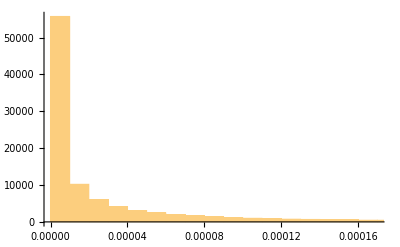

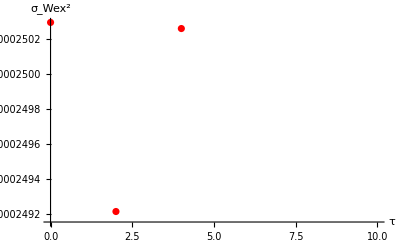

```mathematica
β=1;
λ0=1;
δλ=0.01;

n=200000;
step=2;

datam=List[];
dataσ=List[];
data=List[];

Do[

Do[

qi=RandomVariate[NormalDistribution[0,1/(β λ0)]];
pi=RandomVariate[NormalDistribution[0,1/β ]];

σ=(qi^2 β δλ^2 (λ0 (pi^2+qi^2 λ0) τ^2))/(8 λ0^2 τ^2);

dataσ=AppendTo[dataσ,σ];

,{i,1,n}];

data=AppendTo[data,{τ,Mean[dataσ]-δλ^2/(4β λ0)}];

,{τ,0.001,4.2,step}]

Histogram[dataσ,Automatic,"PDF"]

ListPlot[data,PlotRange->{{0,10},Full},AxesLabel->{"τ","σ_Wex^2"},PlotStyle->Red]
```

Quantum Ising Chain

```mathematica
Clear[g,J]

ϵ[n_]=2J √(1+(g/J)^2-2(g/J)Cos[(2n-1)π/N0]);
u[n_]=(g/J-Cos[(2n-1)π/N0]+ϵ[n]/(2J))/N0;
v[n_]=Sin[(2n-1)π/N0]/N0;

dgH={{-2J(2g/J-2Cos[(2n-1)π/N0])/ϵ[n],0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,2J(2g/J-2Cos[(2n-1)π/N0])/ϵ[n]}};
ρ={{Exp[β ϵ[n]]/(Exp[-β ϵ[n]]+Exp[β ϵ[n]]+2),0,0,0},{0,1/(Exp[-β ϵ[n]]+Exp[β ϵ[n]]+2),0,0},{0,0,1/(Exp[-β ϵ[n]]+Exp[β ϵ[n]]+2),0},{0,0,0,Exp[-β ϵ[n]]/(Exp[-β ϵ[n]]+Exp[β ϵ[n]]+2)}};
(*ρ={{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};*)

Assuming[J>0,Simplify[Tr[dgH.ρ]]]

CdF=Assuming[J>0, Simplify[Tr[dgH.ρ]]]^2;

Limit[CdF,β->Infinity]

CWqs=Simplify[1/2(Tr[dgH.dgH.ρ]+Tr[dgH.ρ]^2)];

Limit[CWqs,β->Infinity]

WqsmdF=Simplify[β/2(Tr[dgH.dgH.ρ]-Tr[dgH.ρ]^2)]

Limit[WqsmdF,β->Infinity]
```

-(2 (-1+ⅇ^(2 β √(g^2+J^2-2 g J Cos[(π-2 n π)/N0]))) (g-J Cos[(π-2 n π)/N0]))/((1+ⅇ^(2 β √(g^2+J^2-2 g J Cos[(π-2 n π)/N0]))) √(g^2+J^2-2 g J Cos[(π-2 n π)/N0]))

ConditionalExpression[(4 (g-J Cos[(π-2 n π)/N0])^2)/(g^2+J^2-2 g J Cos[(π-2 n π)/N0]), √(g^2+J^2-2 g J Cos[(π-2 n π)/N0])>0]

ConditionalExpression[(4 (g-J Cos[((-1+2 n) π)/N0])^2)/(g^2+J^2-2 g J Cos[((-1+2 n) π)/N0]), ]

(4 ⅇ^(2 J β √((g^2+J^2-2 g J Cos[((-1+2 n) π)/N0])/J^2)) β (g-J Cos[((-1+2 n) π)/N0])^2)/((1+ⅇ^(2 J β √((g^2+J^2-2 g J Cos[((-1+2 n) π)/N0])/J^2)))^2 (g^2+J^2-2 g J Cos[((-1+2 n) π)/N0]))

ConditionalExpression[0, ]

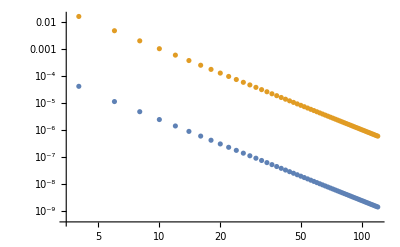

```mathematica
ϵ[n_]=2J √(1+(g/J)^2-2(g/J)Cos[(2n-1)π/N0]);
u[n_]=(g/J-Cos[(2n-1)π/N0]+ϵ[n]/(2J))/N0;
v[n_]=Sin[(2n-1)π/N0]/N0;

δΓ=0.01;
g=0.95;
J=1;

lista=List[];
lista2=List[];

Do[

lista=AppendTo[lista,{N0,16 δΓ^2 Sum[u[n]^2 v[n]^2,{n,1,N0/2}]}];
lista2=AppendTo[lista2,{N0,1/N0^3}];

,{N0,4,120,2}]

ListLogLogPlot[{lista,lista2},PlotRange->Full]
```

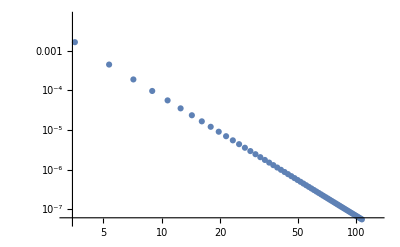

```mathematica
Wqsn[n_]=-2 (√((g0+dg-J Cos[(π-2 n π)/N0])^2+J^2 Sin[((-1+2 n) π)/N0]^2)-√((g0-J Cos[(π-2 n π)/N0])^2+J^2 Sin[((-1+2 n) π)/N0]^2));
```

```mathematica
FullSimplify[Series[Wqsn[n],{dg,0,2}]]
```

-(2 (g0-J Cos[(π-2 n π)/N0]) dg)/(√(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0]))-(J^2 Sin[((-1+2 n) π)/N0]^2 dg^2)/((g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])^(3/2))+O[dg]^3

```mathematica
ΔF=-1/β Log[(Exp[-2β(√((g0+dg)^2+J^2-2 (g0+dg) J Cos[(π-2 n π)/N0]))]+Exp[2β(√((g0+dg)^2+J^2-2 (g0+dg) J Cos[(π-2 n π)/N0]))]+2)/(Exp[-2β(√(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0]))]+Exp[2β(√(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0]))]+2)];

Series[ΔF,{dg,0,2}]
```

-(2 ((-1+ⅇ^(2 β √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0]))) (g0-J Cos[(π-2 n π)/N0])) dg)/((1+ⅇ^(2 β √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0]))) √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0]))-((-J^2+ⅇ^(4 β √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])) J^2+J^2 Cos[(π-2 n π)/N0]^2-ⅇ^(4 β √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])) J^2 Cos[(π-2 n π)/N0]^2+4 ⅇ^(2 β √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])) g0^2 β √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])-8 ⅇ^(2 β √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])) g0 J β Cos[(π-2 n π)/N0] √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])+4 ⅇ^(2 β √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])) J^2 β Cos[(π-2 n π)/N0]^2 √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])) dg^2)/((1+ⅇ^(2 β √(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])))^2 (g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])^(3/2))+O[dg]^3

```mathematica
ΔF = Limit[-1/β Log[(Exp[-2β(√((g0+dg)^2+J^2-2 (g0+dg) J Cos[(π-2 n π)/N0]))]+Exp[2β(√((g0+dg)^2+J^2-2 (g0+dg) J Cos[(π-2 n π)/N0]))]+2)/(Exp[-2β(√(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0]))]+Exp[2β(√(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0]))]+2)],β->Infinity]

Series[ΔF,{dg,0,2}]
```

ConditionalExpression[2 (√(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])-√((dg+g0)^2+J^2-2 (dg+g0) J Cos[(π-2 n π)/N0])), ]

ConditionalExpression[-(2 (g0-J Cos[(π-2 n π)/N0]) dg)/(√(g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0]))+((-J^2+J^2 Cos[(π-2 n π)/N0]^2) dg^2)/((g0^2+J^2-2 g0 J Cos[(π-2 n π)/N0])^(3/2))+O[dg]^3, ]

```mathematica
ΔF = -1/β Log[1/√(1+δλ)];
Wqs = 1/β(√(1+δλ)-1);
Series[ΔF,{δλ,0,2}]
Series[Wqs,{δλ,0,2}]
```

δλ/(2 β)-δλ^2/(4 β)+O[δλ]^3

δλ/(2 β)-δλ^2/(8 β)+O[δλ]^3

```mathematica
Sum[Sin[(π-2 n π)/N0]^2,{n,1,N0/2}]
```

N0/4

```mathematica
s
```